# 1. Preparing files

```mathematica
path="/home/michaszko/Documents/Neutrina/Opus/MINERvA_nu";
type="LFG";
mecDim=24;
eventsNumber=1*10^6;
crossSection=1.19727*10^-39;

Subscript[Δp, T]={75,75,100,75,75,75,75,150,150,150,250,250,1000};
dpT={75,150,250,325,400,475,550,700,850,1000,1250,1500,2500};
dpT2=dpT-Subscript[Δp, T]/2;
Subscript[Δp, L]={500,500,500,500,500,500,500,1000,2000,2000,5000,5000};
dpL={1500,2000,2500,3000,3500,4000,4500,5000,6000,8000,10000,15000,20000};
widthVanilla=Flatten[KroneckerProduct[Subscript[Δp, T],Subscript[Δp, L]]];

lenPT=Length[Subscript[Δp, T]];
lenPL=Length[Subscript[Δp, L]];

(************************************)

mecVanillaDist=Import[path<>"/data/matrix_"<>type<>".dat"];
nonmecVanillaMatrix=Import[path<>"/data/cros_total_nuwro_"<>type<>".dat"];
danielVanillaMatrix=Import[path<>"/data/cros_total_daniel.dat"];
errorVanillaMatrix=Import[path<>"/data/cros_error_daniel.dat"];
covNonVanilla=Import[path<>"/data/daniel_covariance_vanilla.dat"];

(*********************************************)

mecDist=mecVanillaDist/eventsNumber*crossSection*1000000/widthVanilla*12/13;
errorVanillaMatrixError = errorVanillaMatrix/.(y_/;y==0)->1;
covVanilla=PseudoInverse[covNonVanilla];

(**********************************************)

MatrixPlot[Transpose@mecDist];

RectangleChart[
Thread[{Subscript[Δp, T],Take[Plus@@Transpose[mecDist],{#,-1,lenPL}]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Large,
PlotLabel->(#-1)]&/@Range[lenPT-1];

MatrixPlot[Partition[Plus@@mecVanillaDist,mecDim],DataReversed->True,PlotLegends->Automatic];
```

# 2. Test χ^2

## χ^2 bez kowariancji

```mathematica
newVanillaMatrix=Transpose@Partition[mecDist.ConstantArray[1,mecDim^2],lenPL];


x=((danielVanillaMatrix-nonmecVanillaMatrix-newVanillaMatrix)/errorVanillaMatrixError)^2;

χ=Total[x,2]
```

408.71

## χ^2 z kowariancją

```mathematica
newVanillaMatrix=Transpose@Partition[mecDist.ConstantArray[1,mecDim^2],lenPL];
a=Flatten[Transpose[danielVanillaMatrix-nonmecVanillaMatrix-newVanillaMatrix]];
a.covVanilla.a
```

482.185

# 3. Solution

```mathematica
emptyValue=1;

V=Table[Subscript[v, i,j],{i,1,mecDim},{j,1,mecDim}] ;
V1=Flatten@Table[Subscript[v, i,j],{i,1,mecDim},{j,i,mecDim}];
V2=Flatten@Table[Subscript[v, i,j],{i,2,mecDim},{j,1,i-1}];
V3=Flatten[V/.Thread[V2->emptyValue]];

chi2[x_]:=Total[
((danielVanillaMatrix-nonmecVanillaMatrix-Transpose@Partition[mecDist.x,12])/errorVanillaMatrixError)^2,2]

chi2cov[x_]:=(Flatten[Transpose[danielVanillaMatrix-nonmecVanillaMatrix-Transpose@Partition[mecDist.x,12]]]).covVanilla.(Flatten[Transpose[danielVanillaMatrix-nonmecVanillaMatrix-Transpose@Partition[mecDist.x,12]]])

plotMec[x_,fun_]:=MatrixPlot[
Partition[x,mecDim],
PlotLegends->Automatic,
DataReversed->True,
PlotLabel->{"χ_cov^2 = "<> ToString[chi2cov[x]]<>" ,χ_non^2 = " <> ToString[chi2[x]]}]


(*condition[p_]=Module[{a},
a=Join[
Thread[V1≥ 0],
Flatten[Table[Abs[Subscript[v, i,j]-Subscript[v, i,j+1]]/(Subscript[v, i,j]+Subscript[v, i,j+1])<p,{i,1,mecDim},{j,i,mecDim-1}]],
Flatten[Table[Abs[Subscript[v, i,j]-Subscript[v, i+1,j]]/(Subscript[v, i,j]+Subscript[v, i+1,j])<p,{j,1,mecDim},{i,1,j-1}]]];
And@@a];*)

condition[p_]=Module[{a},
a=Join[
Thread[V1≥ 0],
 (*inner elements*)
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}]<1/(1-p),
{i,2,mecDim-1},{j,i+1,mecDim-1}]],

Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}]>(1-p),
{i,2,mecDim-1},{j,i+1,mecDim-1}]],

(*diagonal elements*)
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i-1,j]}]<1/(1-p),
{i,2,mecDim-1},{j,i,i}]],

Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i-1,j]}]>(1-p),
{i,2,mecDim-1},{j,i,i}]],
(*top(bottom) row*)

Flatten[Table[Subscript[v, 1,j]/Min[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}]<1/(1-p),
{j,2,mecDim-1}]],

Flatten[Table[Subscript[v, 1,j]/Max[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}]>1-p,
{j,2,mecDim-1}]],

(*right side*)

Flatten[Table[Subscript[v, i,mecDim]/Min[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}]<1/(1-p),
{i,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Max[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}]>1-p,
{i,2,mecDim-1}]],

{Subscript[v, 1,1]/Subscript[v, 1,2]>1-p,Subscript[v, 1,1]/Subscript[v, 1,2]<1/(1-p),Subscript[v, 24,24]/Subscript[v, 23,24]>1-p,Subscript[v, 24,24]/Subscript[v, 23,24]<1/(1-p)}];

And@@a];

minChi2[fun_,p_,iter_:100,init_:Automatic,print_:False]:=Module[{a,b,c,meth},
meth="PrincipalAxis";
{a,b}=NMinimize[
{fun[V3],condition[p]},
V1,
MaxIterations->iter,
Method->{"RandomSearch","SearchPoints"->1,"RandomSeed"-> RandomInteger[1000],Method->meth,"InitialPoints"->init},

StepMonitor:>(
Export[path<>"/results/chi2Values/"<>ToString[fun]<>"_"<>ToString[fun[V3]]<>"_maxIter_"<>ToString[iter]<>"_continuous_"<>ToString[p]<>"_"<>meth<>".dat",Partition[V3,mecDim]];

If[print==True,Print[plotMec[V3,fun]]])
];

Export[path<>"/results/chi2ValuesFinal/"<>ToString[fun]<>"_"<>ToString[fun[V3/.b]]<>"_maxIter_"<>ToString[iter]<>"_continuous_"<>ToString[p]<>"_"<>meth<>".dat",Partition[V3/.b,mecDim]];

c=chi2[V3/.b];
{a,c}
]
```

## χ^2 with covariance

### χ^2 vs continuity parameter

```mathematica
list2=Parallelize[Thread[{minChi2[chi2cov,#,10],#}]&/@Range[0.1,1,0.1]]
Export[path<>"/chi2_vs_con_InteriorPoint_100_2.dat",%];
```

```mathematica
list1={{{305.4706495850406,0.1},{335.36567215682106,0.1}},{{251.4232213564077,0.2},{264.75507177247255,0.2}},{{239.12573154072723,0.30000000000000004},{289.60112410576903,0.30000000000000004}}};
```

```mathematica
listCov=First[#]&/@list;
listNonCov=Last[#]&/@list;
ListPlot[%]
ListPlot[%%%]
```

### Covergence

```mathematica
(*covergence=Parallelize[Thread[{minChi2[chi2cov,0.3,10],#}]&/@Range[15]]*)
covergence={{{295.82351376529397,1},{442.8834336369929,1}},{{253.2928795509696,2},{630.1689189550752,2}},{{253.3058097568018,3},{631.0269998505345,3}},{{254.10381311685893,4},{612.2297191983799,4}},{{253.2928795645396,5},{630.1689187896461,5}},{{253.2931986440668,6},{630.1773238474018,6}},{{253.29316350456145,7},{630.2009217421398,7}},{{253.46145423861316,8},{626.6673598421949,8}},{{253.29306911034845,9},{630.1675506604466,9}},{{296.78891210472943,10},{438.42917221475983,10}},{{253.2938269758273,11},{630.1867408084054,11}},{{253.63601940065448,12},{627.7224847828168,12}},{{253.29410823654274,13},{629.090667160411,13}},{{253.29287955187712,14},{630.1689187459344,14}},{{295.08678972355636,15},{448.600229032898,15}}};
```

```mathematica
First[First[#]]&/@covergence//ListPlot
First[Last[#]]&/@covergence//ListPlot
(*Export[path<>"/chi2_vs_con_0.3_InterialPoint_maxIter_100_15.dat",covergence]*)
```

### Covergence 2

```mathematica
covergence=Parallelize[Thread[{minChi2[chi2cov,0.3,100],#}]&/@Range[5]]
```

```mathematica
{{{254.35504234464753,1},{599.9403696377249,1}},{{253.29288117513502,2},{630.1682464723431,2}},{{269.08882605475765,3},{662.6502055444145,3}},{{268.8949021712116,4},{664.3738088297241,4}},{{253.60038653208724,5},{620.9743435846935,5}}}
```

```mathematica
First[First[#]]&/@covergence//ListPlot
First[Last[#]]&/@covergence//ListPlot
```

### Normal

```mathematica
(*low=Import [path<>"/results/chi2ValuesFinal/chi2cov_324.442_maxIter_100_continuous_0.4_InteriorPoint.dat"];
low=Flatten[low/. 1->Nothing];
minChi2[chi2cov,0.4,100,{low}]*)
minChi2[chi2cov,0.2,100]
minChi2[chi2cov,0.2,100]
```

$Aborted

$Aborted

# 4. Plots of result

```mathematica
Needs["ErrorBarPlots`"]
tmp=Import ["/home/michaszko/Documents/Neutrina/Opus/MINERvA_nu/results/chi2ValuesFinal/tomek_final.dat"];

q=Flatten[Transpose@nonmecVanillaMatrix];
w=Flatten[Partition[mecDist.Flatten[ConstantArray[1,24^2]],12]];
v=Flatten[Partition[mecDist.Flatten[tmp],12]];

bb=
Flatten[Transpose@nonmecVanillaMatrix+Partition[mecDist.Flatten[tmp],12]];
cc=
Flatten[Transpose@danielVanillaMatrix];

lol1=Flatten[Thread[{dpT2,Take[cc,{#,-1,lenPL}]}]&/@Range[lenPL],1];
lol2=ErrorBar[#]&/@Flatten[errorVanillaMatrix];
dd=Partition[Thread[{lol1,lol2}],13];

a=RectangleChart[
Thread[{Thread[{Subscript[Δp, T],Take[q,{#,-1,lenPL}]}],Thread[{Subscript[Δp, T],Take[w,{#,-1,lenPL}]}]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Full,
ChartStyle->{Red,Yellow},
PlotLabel->Text[Style["CC 0π ν_μ, MINERvA_nu, NuWro before rescaling, " <> ToString[dpL[[#]]]<>" < p_L < "<>ToString[dpL[[#+1]]] <> " [MeV]"(*",\n χ_cov^2 = " <> ToString[chi2cov[ConstantArray[1,mecDim^2]]]<>" , χ_noncov^2 = " <> ToString[chi2[Flatten[tmp]]]*) ,FontSize->17]],
FrameLabel->{Text[Style["p_T [MeV]",FontSize->17]],Text[Style["cross section (per nucleon) [cm^2/GeV^2/nucleon]",FontSize->17]]},
Frame->True,
Axes->False,
Background->White,
ChartLayout->"Stacked",
ChartStyle->EdgeForm[None],
ColorFunction->(EdgeForm[None]&),
PlotRange->{{0,Last[dpT]},Automatic},
ChartLegends->Placed[{Text[Style["non-MEC",Large]],Text[Style["MEC",Large]]},{Right,Top}],
PlotLabel->(#-1)]&/@Range[lenPL];

b=RectangleChart[
Thread[{Thread[{Subscript[Δp, T],Take[q,{#,-1,lenPL}]}],Thread[{Subscript[Δp, T],Take[v,{#,-1,lenPL}]}]}],
GridLines->Automatic,
BarSpacing->None,
ImageSize->Full,
ChartStyle->{Red,Yellow},
PlotLabel->Text[Style["CC 0π ν_μ, MINERvA_nu, NuWro after rescaling, " <> ToString[dpL[[#]]]<>" < p_L < "<>ToString[dpL[[#+1]]] <> " [MeV]"(*",\n χ_cov^2 = " <> ToString[chi2cov[Flatten[tmp]]]<>" , χ_noncov^2 = " <> ToString[chi2[Flatten[tmp]]]*),FontSize->17]],
FrameLabel->{Text[Style["p_T [MeV]",FontSize->17]],Text[Style["cross section (per nucleon) [cm^2/GeV^2/nucleon]",FontSize->17]]},
Frame->True,
Axes->False,
Background->White,
ChartLayout->"Stacked",
ChartStyle->EdgeForm[None],
ColorFunction->(EdgeForm[None]&),
PlotRange->{{0,Last[dpT]},Automatic},
ChartLegends->Placed[{Text[Style["non-MEC",Large]],Text[Style["MEC",Large]]},{Right,Top}],
PlotLabel->(#-1)]&/@Range[lenPL];

c=ListStepPlot[
Thread[{dpT,Take[cc,{#,-1,lenPL}]}],
Left,
GridLines->Automatic,
Joined->False,
ImageSize->Full,
PlotStyle->{Black,Thickness[0.004]},
DataRange->{0,Last[dpT]},
PlotLabel->(#-1)]&/@Range[lenPL];


d=ErrorListPlot[
dd[[#]],
GridLines->Automatic,
ImageSize->Full,
DataRange->{0,Last[dpT]},
PlotStyle->{Black,Thickness[0.002],PointSize[0]},
PlotLabel->(#-1)]&/@Range[lenPL];

(*Show[{a[[#]],c[[#]],d[[#]]}]&[1]*)

Export[path<>"/plots/histogramsBefore/"<>ToString[#]<>".pdf",Show[a[[#]],c[[#]],d[[#]]]]&/@Range[lenPL];
Export[path<>"/plots/histogramsAfter/"<>ToString[#]<>".pdf",Show[b[[#]],c[[#]],d[[#]]]]&/@Range[lenPL];
(*Export[path<>"/plots/histogramsTogether/"<>ToString[#]<>".pdf",Show[{a[[#]],b[[#]],c[[#]],d[[#]]}]]&/@Range[lenPL];*)
```

# 5. Tests

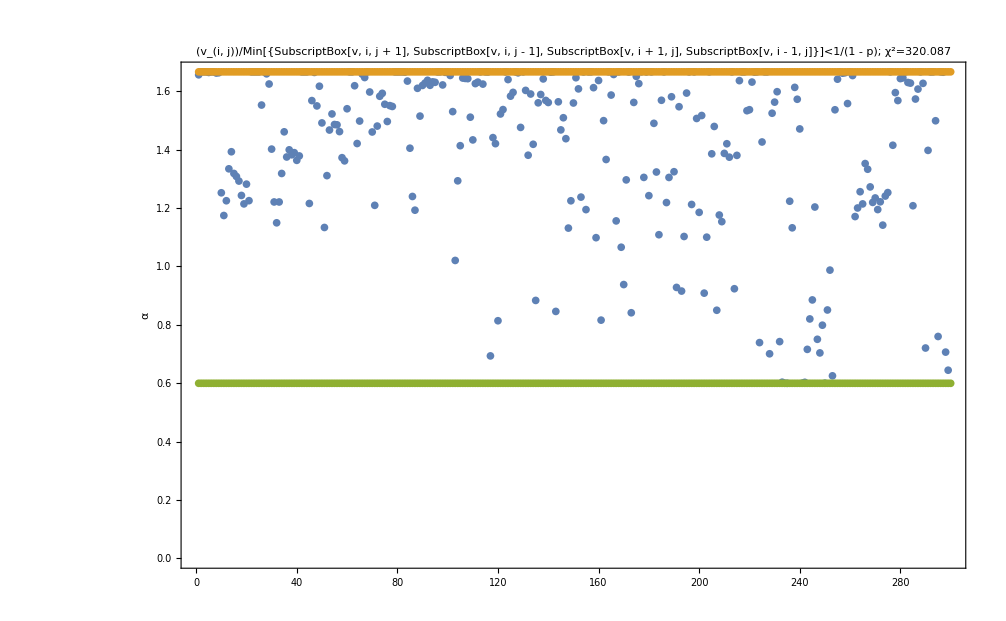

1

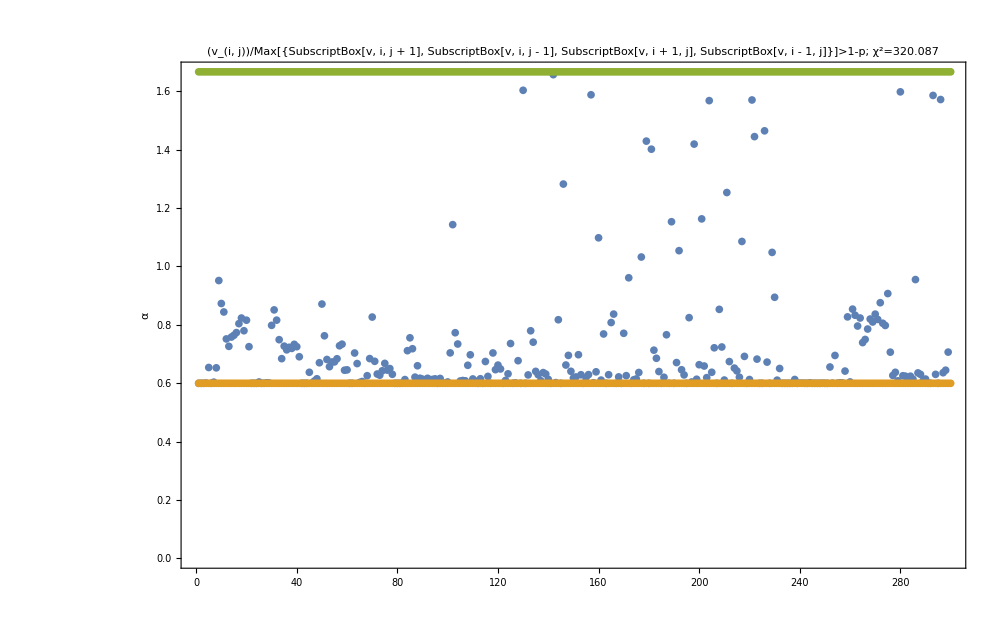

1

```mathematica
tmp2=Import [path<>"/results/chi2Values/chi2cov_324.442_maxIter_100_continuous_0.4_InteriorPoint.dat"];
tmp3=Flatten[tmp2/. 1->Nothing];
var=Thread[V1->tmp3];
p=0.4;

Join[
Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i+1,mecDim-1}]],


Flatten[Table[Subscript[v, i,j]/Min[{Subscript[v, i,j+1],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i,i}]],


Flatten[Table[Subscript[v, 1,j]/Min[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}],
{j,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Min[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}],
{i,2,mecDim-1}]],


{Subscript[v, 1,1]/Subscript[v, 1,2],Subscript[v, 24,24]/Subscript[v, 23,24]}]/.var;

ListPlot[
{%,ConstantArray[1/(1-p),300],ConstantArray[1-p,300]},
PlotLabel->"(v_(i, j))/Min[{SubscriptBox[v, i, j + 1], SubscriptBox[v, i, j - 1], SubscriptBox[v, i + 1, j], SubscriptBox[v, i - 1, j]}]<1/(1 - p);  χ^2=320.087",
Frame->True,
FrameLabel->{,α},
PlotRange->All]

Count[Thread[%%≤1/(1-0.4)],False]



Join[
Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i,j-1],Subscript[v, i+1,j],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i+1,mecDim-1}]],


Flatten[Table[Subscript[v, i,j]/Max[{Subscript[v, i,j+1],Subscript[v, i-1,j]}],
{i,2,mecDim-1},{j,i,i}]],


Flatten[Table[Subscript[v, 1,j]/Max[{Subscript[v, 1,j+1],Subscript[v, 1,j-1],Subscript[v, 1+1,j]}],
{j,2,mecDim-1}]],


Flatten[Table[Subscript[v, i,mecDim]/Max[{Subscript[v, i,mecDim-1],Subscript[v, i-1,mecDim],Subscript[v, i+1,mecDim]}],
{i,2,mecDim-1}]],


{Subscript[v, 24,24]/Subscript[v, 23,24],Subscript[v, 1,1]/Subscript[v, 1,2]}
]/.var;

ListPlot[
{%,ConstantArray[1-p,300],ConstantArray[1/(1-p),300]},
PlotLabel->"(v_(i, j))/Max[{SubscriptBox[v, i, j + 1], SubscriptBox[v, i, j - 1], SubscriptBox[v, i + 1, j], SubscriptBox[v, i - 1, j]}]>1-p;  χ^2=320.087",
Frame->True,
FrameLabel->{,α},
PlotRange->All
]

Count[Thread[%%≥0.6],False]
```

```mathematica
tomek=Import[path<>"/results/chi2ValuesFinal/tomek.dat"];
chi2cov[Flatten@tomek]
```

360.993

```mathematica
q=Flatten[Transpose@nonmecVanillaMatrix];
w=Flatten[Partition[mecDist.Flatten[ConstantArray[1,24^2]],12]];
Thread[{q,w}];
```